```mathematica
<<MathWorld`Fourier`
```

```mathematica
getCoefs[k_,L_]:=(
expr=FourierPartialSums[Exp[-x^2/2.],{x,-Pi L,Pi L},k]//Last;
Cases[expr,Times[a_,Cos_]:>a]
);

plotCoefs[k_,L_]:=ListPlot[getCoefs[k,L],PlotStyle->Directive[PointSize[Large],Magenta],PlotRange->All];

plotFourier[k_,L_]:=Plot[Exp[-x^2/(2 L^2)]/L,{x,0,k},PlotRange->All]
```

```mathematica
doPlot[L_]:=(
plot1=plotFourier[10L,L];
plot2=plotCoefs[10L,L];
Show[plot1,plot2,PlotLabel->"integral limit "<>ToString[L]<>" pi"]
)
```

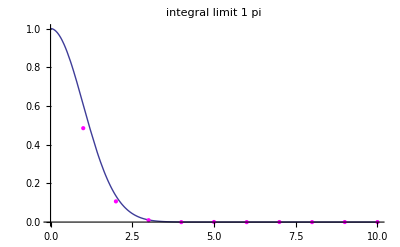

```mathematica
doPlot[1]
```

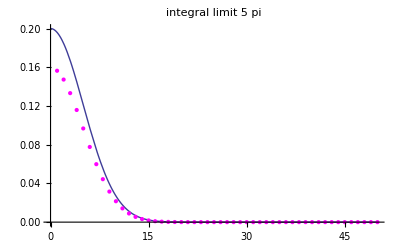

```mathematica
doPlot[5]
```

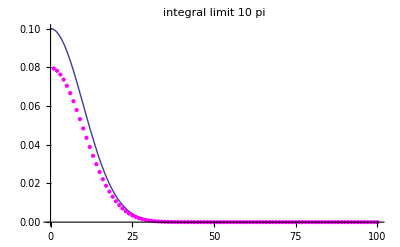

```mathematica
doPlot[10]
```

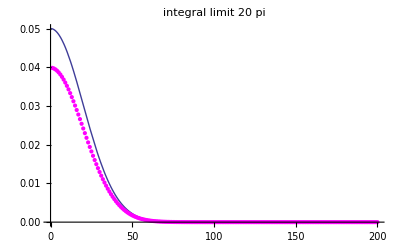

```mathematica
doPlot[20]
```